# PGSC Wildcat’s Guide To Mathematica

## 0. Introduction

Welcome to Kansas State! This is a guide originally intended to help new physics graduate students become familiar with Mathematica. Mathematica is a powerful tool that some professors will require you to use for classes. It can also help you in research for things like, plotting, data analysis, and other heavy computations. 

This guide is by no means extensive, it will mostly cover the basics of syntax and provide some useful tips and examples. In the future (hopefully), there will be some more details on formatting, styling, and typesetting. Note that this guide was written using Wolfram 15.0 on Windows and Linux, so some things may have changed depending on what version you are using.  On windows/Linux you can toggle fullscreen by pressing F12. For Mac OS, the fullscreen toggle is either Cmd + Opt + F or Ctrl + Cmd + F.

Another thing you will want to make sure is enabled is Dynamic Updating. This can be found under the Evaluation menu. Ensure that the box by Dynamic Updating Enabled  is checked as some of the features in this guide depend on Dynamic Updating. It should be on by default, but occasionally Mathematica will have run into an error and disable Dynamic Updating, so you may have to re-enable it.   

Throughout this guide, there are sections with drop-down arrows (-Graphics-), Click them to expand and hide the sections below. 
There will also be exercises with input boxes that look like this:

```mathematica
(*Your code here*)
```

Here, you can practice writing your own code. Possible solutions to exercises will also be included. 

This is a work-in-progress.  Currently, only the first 3 sections are completed. I hope to have the rest completed soon, you can find the latest updates and progress on the GitHub page.
If you have any issues, questions, or suggestions, please reach out to me at mattallp@ksu.edu or over Discord. 
Hopefully, you will find this guide helpful! 

-Matthew Allphin, PGSC Academic Chair 2026-2027

## I. Basics

This section covers basics. This includes things like, how to write and evaluate code, how to declare variables, and how to call functions.

### Input and Output

Editable Mathematica files are called notebooks, you can create them either from the start screen when you open Mathematica or by going to File and selecting New. When you create a new notebook, it probably won’t look like this notebook. This is because I am using the StandardReport stylesheet for this notebook which can be found under the Format tab under Stylesheet. 

 In your computer files, notebooks are denoted by the .nb extension. Make sure you SAVE OFTEN as there is no auto-save feature for Mathematica and if your program crashes, there is no way to recover the files if they aren’t saved. The quickest way to do this is using the Ctrl + S shortcut. The undo (Ctrl + Z) and redo (Ctrl + Y) command can also be very helpful. 

There are two main kinds of code blocks in a Mathematica notebook. First there are input cells

```mathematica
7 (*Input cell*)
```

These cells allow you to input your code and run them. In order to run a cell of code, you need to select the cell you want to run by clicking in the cell (your text cursor will appear in the cell)  and press Shift + Enter on the Keyboard. Try this below:

```mathematica
7  (*Click on the cell and press Shift+Enter on your keyboard*)
```

If you have done this correctly, Mathematica will generate an output cell:

7

You can also evaluate all cells at the same time in your notebook by clicking the -Graphics-  in the top left corner. 
There is also a drop-down menu which will allow you to evaluate a single cell. For most of this tutorial, you will want to evaluate the input cells as you go. 
You can also select cells using the brackets on the right-hand side of the notebook: -Graphics-.Notice that on the left-hand side these boxes are labeled: In[#]= & Out[#]=

These can be used both to label your code and recall things for later use:

```mathematica
Out[4](*gives code form Out[4]*)
```

You can also use % to for the last evaluated output:

```mathematica
%
```

Be careful, however, as this will give you the last evaluated output not the output directly above.
You can also separate cells by going clicking in the cell and pressing Ctrl + D.

#### Clearing and Suppressing Output

Mathematica will output each and every line of evaluated code. For large data sets and complicated numerical calculations, this can be cumbersome. However, we can suppress output by using a semi-colon ;

Try evaluating the code below and notice that Mathematica will not generate an output cell

```mathematica
15851910237+ 120957;
```

However, the cell still evaluated and we can call the value that Mathematica calculated using %

```mathematica
%
```

We can also delete outputs by selecting the output cell bracket found on the right hand side, -Graphics-, pressing the delete key. To delete all output, you can got to the Cell tab and click Delete All Output.

#### Documentation

Mathematica has a large library of documentation including which is easily accessible by going to the Help tab and clicking the documentation. You can also press the F1 key and it will bring you to the documentation home page. If you highlight over text and press the F1 key, it will search the Mathematica documentation for your highlighted text. 

If you chose to download the documentation locally, you will not need access to the internet in order to navigate the documentation. In addition, the documentation includes a number of interactive notebook tutorials that you can access from the homepage and open directly in Mathematica. If you do not have the documentation installed, trying to open the documentation in Mathematica will open the documentation in your web browser. There, you can also download other Mathematica tutorials from the documentation. 

If you are ever unsure of how to do something in Mathematica, check the documentation. If that doesn’t work, searching online can also help as there is a widespread community of Mathematica users.

#### Errors

When Mathematica is unable to perform an action, it will still give an output. However, it will also give an error. As an example, Evaluate the code below to see what it looks like:

```mathematica
1/0 (*generates an error*)
```

You should see some error text: Power::infy: "Infinite expression 1/0 encountered.".  The three dots will allow you too look more closely at what the error is and the little blue icon will link you to the Mathematica documentation associated with that error. 

Notice also that Mathematica still gave the output “ComplexInfinity” which is technically correct, but ultimately the answer should be “undefined”.

#### Troubleshooting

There are a few different tools you can use to troubleshoot/debug your code. We will include some details on how to do this a bit later in the guide. However, there are a couple basic troubleshooting tools we will are going to introduce now as they are essential.

The first tool is the Abort command.  Once you tell Mathematica to evaluate a code cell, it will not evaluate any other code until after the code cell has finished evaluating. This can be problematic if you need to make a change to your code while it is evaluating or if you have made a mistake somewhere.  For example, if you have a block of code that includes an infinite loop, you will not be able to make any changes until Mathematica goes through enough iterations to overflow the memory. 

The Abort command is the failsafe that allows you to stop Mathematica mid-evaluation.  You can use the Abort command mid-evaluation by either clicking the abort button at the top left of the screen -Graphics-, or you can press Alt + . on your keyboard. Below, I have programmed an infinite loop. Try evaluating it and then using the Abort command (Alt + .) to stop the evaluation:

```mathematica
While[0<1,
k=2;
]
```

A couple things to note, for some keyboards the abort command only works for the LEFT Alt key. Notice also on the right-hand side that the cell bracket becomes bold when Mathematica is evaluating code. 

The final tool we will introduce here is the quit Kernel command. It isn’t super important that you understand what the Kernel is or why it needs to be restarted. What you do need to know is that this command is basically the “Turn it off and turn it on again” solution in Mathematica. You can access this command by simply evaluating the command Quit[] in an input cell or by going to the toolbar on the top left of the window and going to Evaluation > Quit Kernel > Local. 

Keep in mind that this will clear any and all variables and outputs you have declared from memory, so you will have to re-evaluate all of that code again if you are using them. The main thing to remember is this: If you are not sure what could be wrong with your code, try quiting the kernel.  We will go over the basics of debugging in Section IV.

#### Comments in code

While Mathematica allows you to type in text boxes which will not evaluate as code, it is still good practice to include comments in your input boxes. Mathematica uses (* *) to denote comments:

```mathematica
(*Comments that won't be evaluated as code*)
```

You can also highlight text and then press Alt + ? to comment in/out a block of code

### Variables and Basic Functions

Like other programming languages, Mathematica allows you define variables by writing <VariableName> = <value>:

```mathematica
variable = 20; (*define the variable *)
variable  (*output variable value*)
```

Be careful when naming your variables as Mathematica has some pre-defined constants. Attempting to declare pre-defined constants as a variable will result in in error. One way you can tell whether or not a function is already defined is by the color of the text. Undefined variables are in light blue, while defined variables are in white. Mathematica also has a way for you to look-up constants and even handle physical units, which we will address later in this guide. (REF?)

```mathematica
myVar (*notice the text is blue because the variable hasn't been defined*)
Pi (*The ratio of the circumference of a circle to its diameter*)
I (**)

Pi= 3(*error generated when trying to define Pi = 3*)
```

Once you have defined and evaluated variables you can use them at any point in your calculations. Mathematica can perform any basic calculator functions using the standard characters on your keyboard: + (add), - (subtract), * (multiply), / (divide), ^ (exponent). Try defining a few variables below and performing these simple operations:

```mathematica
(* Your code here*)
```

Mathematica also allows for typesetting within the code. This allows for cleaner looking input. For example, using Ctrl + / will create a fraction bar where you can write code in the numerator and the denominator. Ctrl + 6 will allow you to input superscripts which behave as exponents when evaluated. There are also a number of other typesetting tricks, and we will touch upon them more in Section II.  Here are some examples, feel free to mess with them or try something out.

```mathematica
3/4 (*Create a fraction bar using ctrl + /*)

2^2(*create an exponet using ctrl + 6*)
```

Of course, just like your calculator, Mathematica also do more complex and specific calculations using pre-defined functions. Functions in Mathematica have the form Function[<parameters>]. Notice, the pre-defined function is always capitalized! Your parameters will depend on which function you are using, if you are not sure what parameters you need look for the documentation of the command using F1 or clicking -Graphics-. Common calculations such as sine, cosine, square root, and logarithms are pre-defined in Mathematica. For the most part, they work as you would expect:

```mathematica
Sin[Pi/2] (*sin of π/2*)
Cos[Pi] (*sin of π*)
Sqrt[4] (*Sqrt of 4*)
```

However, even basic functions have some nuances. For example, Mathematica always assumes that the input is in Radians instead of degrees. One way to remedy this is to use the Degree constant which is just equal to π/180. Using this appropriately will switch between degrees and radians:

```mathematica
Sin[45 Degree] (*Sin of 45^*)
Sin[45] (*Sin of 45 Radians*)
```

You may have also noticed that the output above is exact, meaning there are no decimal approximations. This is because Mathematica will always try to give an exact solution unless told to do a numerical approximation. This can be helpful since Mathematica will also try to simplify symbolic expressions. However, when dealing with actual data you will likely want actual numerical values. This can be remedied using the N[] command.  This command will default to storing as many digits as possible, but you can also tell Mathematica to only keep a certain number of digits by adding a parameter. Note that using N[] without extra parameters will not necessarily output all of the stored digits. You can show all the digits by selected the output cell and clicking “show all digits”.

```mathematica
N[Sqrt[2]] (*numerical value of the square root of 2, Mathematica will only output 6 digits, but actually has evaluated a lot more digits*)

N[Sqrt[2],3] (*numerical value of square root of 2 up to 3 digits, mathematica will both output and store the exact value*)

N[Sqrt[2],10](*numerical value of square root of 2 up to 10 digits*)
```

Note also that once a decimal approximation is calculated, using it in any other calculation will result in Mathematica giving a decimal approximation:

```mathematica
var = N[Pi] (*numerical value of π*)
2* var (*gives numerical value of 2 π*)
2 * Pi (*gives exact expression for 2 π*)
```

As a final note, you can clear variable values using the Clear[] command, and doing Clear[“`*”], will clear all variables in the notebook.

```mathematica
Clear[var] (*clears var from memory*)
Clear["`*"] (*Clears all variables from memory*)
```

Now, let’s let you put some of this to use with an exercise.

#### Exercise

The Log[] command for logarithms also defaults to the natural log, and you can either use the change-of-base formula, or a Mathematica command. Try to see if you can calculate Log_2(2365) below to 5 digits, don’t forget to look at the documentation (F1) if you are unsure what to do.

```mathematica
(*Your code here*)
```

#### Solution

The documentation indicates that the log command requires an extra input if I want to change the base Log[base,value], and then we can use N to give 3 digits. You can either do this in multiple command lines:

```mathematica
Log[2,2365] ;(*Subscript[Log, 2](2365)*)
N[%,3] (*get three digits of the previous output*)
```

Or in one command line:

```mathematica
N[Log[2,2365],3] (*get three digits of Subscript[Log, 2](2365)*)
```

### Lists, Vectors, and Matrices

Mathematica can also define lists using  curly braces {} where each element is separated by a comma,

```mathematica
list = {1,2,3,4,5,6,7}
```

You can access the elements of a list using double square braces [[#]], where # is the position you wish to access. note that the list begins indexing at 1. Using the index -1 will give the last item in the list, you can also get sublists by using ;;. For example list[[2;;]] will return a sublist beginning from the second element until the last element:

```mathematica
list[[1]] (*returns the item in the first position*)
list[[-1]] (*returns the item in the last position*)
list[[2;;]] (*returns a sublist excluding the first element in the list*)
```

You can also define a nested list, and you will then have to use two different indices to determine which element you want to access.

```mathematica
nestedList = {{1,2,3},{4,5,6}};
nestedList[[1,3]] (*returns the third element in the first list, the number 3*)
nestedList[[1]] (*returns the entire first list*)
nestedList[[;;,1]]  (*returns then first element of each list*)
```

Similar to other variables, you can also perform operations on lists of the same length. You can apply the same operation on all elements of the list at once

```mathematica
(*define lists*)
listA = {1,2,3,4} ;
listB= {-2,4,-6,8};

(*do elementwise operations*)
listA + listB
listA * listB

(*multiply each element on the list by 2*)
2* listA
(*subtract 2 from each element of the list*)
listA - 2
```

In general, using a function on a list will apply that function on each element of a list:

```mathematica
list = {1,2,3}; (*define list*)
Sqrt[list]
```

There are some functions which are designed to work with lists. For example, passing a list to the Sort function will output the sorted list:

```mathematica
myList = {3,8,9,10,3,5,1,2} (*define a list*)
Sort[myList] (*sort list*)
```

Other useful commands are things like the Total[], Mean[], and StandardDeviation[] commands. We will go over these kinds of operations more in section V.

Lists can also work as vectors, and you can calculate the standard dot product by either using the Dot[] command or simply using a period as a multiplication symbol:

```mathematica
A = {1,1,1} (*define vectors*)
B = {1,-1,1} 
A.B (*calculate dot product*)
```

You can also define matrices using nested lists, and you can perform matrix multiplication again using the Dot[] command. You can also ask Mathematica to display lists and nested lists as column vectors and matrices using the MatrixForm[] command.

```mathematica
M = {{0,1},{1,0}}; (*define the matrix*)
v = {1,0}; (*define a vector*)
(*display M as a matrix and v as a column vector*)
MatrixForm[M]
MatrixForm[v]

MatrixForm[M.M ](*multiply the matrix by itself*)
MatrixForm[M.v](*Apply the matrix M to the vector A*)
```

Note that using the MatrixForm command turns your list into something else. Therefore, if you try to define a variable using MatrixForm, it will prevent you from performing operations on the matrix:

```mathematica
notAMatrix = MatrixForm[{{1,0},{0,1}}] (*stores the MatrixForm of the matrix*)
notAVector = MatrixForm[{1,0}] (*stores the MatrixForm of the vector*)
notAMatrix.notAVector (*doesn't do the actual calculation*)
```

Mathematica can also do a number of matrix calculations such as row reduction, eigenvalue and eigenvector calculations, determinants, inverses, etc.:

```mathematica
mat = {{1,2,3,4},{5,6,7,8},{9,10,11,12},{13,14,15,16}}; (*a matrix*)

Det[mat] (*calculate the determinant*)
NullSpace[mat] (*returns the vectors which span the null space of the matrix*)
```

We will end this section with an exercise.

#### Exercise

In the Input cell below, I have defined an example matrix, H. Use the Mathematica documentation to find the eigenvalues, eigenvectors, and an orthogonal basis for the eigenspace (you may find the commands Eigenvalues[], Eigenvectors[], Eigensystem[], and Orthogonalize[]).

```mathematica
H=N[ {{1,1,2},{-1,5,2},{2,-1,4}}] (*H matrix*)

(*your code here*)
```

#### Solution

There are multiple ways to do this, but here is one possibility:
The eigensystem command will return both the eigenvalues and the associated eigenvectors:

```mathematica
eigenSolution = Eigensystem[H] (*find the eigenvectors and eigenvalues*)
```

To find an orthogonal basis, I can use the Orthogonalize command on the 2nd list of eigenSolution

```mathematica
orthogonalVectors= Orthogonalize[eigenSolution[[2]]]
```

To check to make sure they are orthogonal, we can calculate their inner products. Notice that the not all inner products are not exactly zero, this is due to the roundoff error that occurs during the numerical calculation. However, the numerical outputs are on the order of 10^-17, which is basically zero. The orthogonalize command also returns normalized vectors

```mathematica
(*calculate the inner product to show the vectors are orthogonal*)
orthogonalVectors[[1]].Conjugate[orthogonalVectors[[2]]] 
orthogonalVectors[[1]].Conjugate[orthogonalVectors[[3]]] 
orthogonalVectors[[3]].Conjugate[orthogonalVectors[[2]]] 
(*the resulting vectors are also orthonormal*)
Table[Norm[orthogonalVectors[[j]]],{j,1,3}]
```

## II. Functions and Numerics

This section covers how to define and evaluate functions in Mathematica as well as some nuances of the numerical calculations and units in Mathematica.

### Function Definition

As discussed in the previous section, Mathematica has a wide variety of pre-built functions and commands that you can use to do all sorts of calculations. While we will introduce you to some useful pre-built functions throughout this guide, anything you will ever need to know how to use pre-built functions can be found in the documentation or through an online search.

Our focus in this section is how to define your own functions in Mathematica. The syntax for defining a function in Mathematica is similar to that of defining variables:

Function[var1_, var2_, ...] = <your function here>

Notice that for each variable (var#) must have an underscore after it if you want Mathematica to recognize it as a function variable. 

Once you have defined a function this way, you can call it like you would any other function:

```mathematica
f[x_,y_]= x^2 +y^2(*Define the function*)
f[2,0] (*returns f(2,0)*)
f[w,z] (*will return the function in terms of w and z*)
```

You can even use functions in other function definitions:

```mathematica
Clear[f] (*Clear the function f*)
f[x_]= Cos[x]Sin[x] 

g[x_]= x^2 f[x]
```

Notice also that when multiplying variables, I do not need to use * symbol. If I simply put a space between two symbols, Mathematica will understand that I want to multiply them.

Functions defined have some useful built-in properties. For example, the derivative command D[], has a shortcut for single variable functions:

```mathematica
Clear[f,g] (*clear previous function definition*)
g[x_]= Exp[x]Sin[x] (*define a function*)
D[g[x],x] (*calculate the first derivative of the function*)
g'[x](*Another way to claculate the first derivative of the function*)
```

You can also define vector functions and perform various differential operators on both scalar and vector functions. Mathematica can also handle differential operators in different coordinate systems, but you need to specify them.

```mathematica
G[x_,y_,z_] = {y^2 + z, x^3, 3y } ;(*define a vector function*)
h[r_,theta_,phi_] = 3 r^2 Cos[phi]^2 Sin[theta] + 4 r^3 Cos[phi];(*define a scalar function in spherical coordinates*)

Grad[h[r,theta,phi],{r,theta,phi},"Spherical"](*Gradient in Spherical coordinates, note that the second coordinate is the polar angle, and the third coordinate is the azimuthal angle*)

Curl[G[x,y,z],{x,y,z}](*Curl*)

Div[G[x,y,z],{x,y,z}](*Divergence*)

Laplacian[h[r,theta,phi],{r,theta,phi},"Spherical"] (*Laplacian*)
```

Being able to define functions in this way can be very helpful. Especially when it comes to creating nice plots, we will get to more of plotting in section III. 

At this point, I also want to introduce you to a slightly different way to declare functions and variables using SetDelayed , or the colon-equals (:=)  command.  With a normal equals sign, you cannot edit your function in any way once you have defined it. For example, suppose I have some quadratic polynomial . Where a, b, and c, are some constants. If I define the function first using equals (=), and then make changes to the constants, I the function will not change unitl I re-define it:

```mathematica
Clear[a,b,c,h] (*Clear variable names*)
(*give a, b , and c values*)
a=1;
b=2;
c=3;
h[x_]= a x^2 + b x + c(*define a function h(x) using =*)
```

```mathematica
(*change the values of a, b and c*)
a=2;
b=0;
c=0;

h[x]  (*still prints out the function h(x) with a=1, b=2, c=3 instead of the new values*)
```

This happens because when I use =, Mathematica evaluates the function definition only when I execute the cell containing the definition. However, I can use a delayed function definition so that Mathematica will evaluate the definition each time the function is called. Using the same example as before, I can now change the values of a, b, and c at any time:

```mathematica
Clear[a,b,c,h] (*Clear variable names*)
h[x_]:= a x^2 + b x + c(*define a function h(x) using =*)
```

```mathematica
a=1; (*define a,b, and c*)
b=2;
c=3;

h[x]

(*Change the values of a, b, and c*)

a=2; (*change a,b, and c*)
b=0;
c=0;

h[x]
```

Note that since Mathematica didn’t actually evaluate my function definition when I defined it, there is no output until I call the function in the second cell block. There are advantages and disadvantages to using  = and :=.  You will get a better feeling for them as

#### To finish of this section on function definition, we will try an exercise.

#### Exercise

Using a function definition, try to find the first order zero of the function  where  and  are the zeroth order Bessel functions of the first and second kind, respectively. You may need to look up the documentation on the commands BesselJ[], BesselY[], and FindRoot[]. Also note that when you want to define a condition, you need to use a double equals sign (==) as you are not trying to define a variable

```mathematica
Clear["`*"] (*Clear all variables*)
(*Your code here*)
```

#### Solution

I can define the function using the pre-built Mathematica functions for the Bessel functions

```mathematica
Clear["`*"] (*Clear all definitions*)

f[x_] = BesselJ[0,x]- BesselY[0,x];
```

There are a couple of ways I can find the first zero, if I use the FindRoot command, I need to specify where I want the to look by defining . Since I know that the function is singular at , I will chose

```mathematica
FindRoot[f[x]==0,{x,0.01}]
```

### Replace

Now, we are going to introduce a couple of different ways Mathematica processes functions. We’ll mainly be focusing on some nuances of the syntax for a few different commands and explaining how Mathematica interprets them. Unfortunately, you will most likely have to learn through experience when to use the techniques presented here. 

The first command we want to introduce is the Replace command, denoted using slash-dot (/.). The replace command can replace symbols or placeholders with actual values. This can be useful if you want to have the symbolic expression readily available but still want to get numbers for specific parameters.  

In order to use the Replace command, we also need what is called a rule. Rules take the form, <parameter> ->  <value>. The -> (dash-greater-than) symbol should turn into an arrow in Mathematica’s input cell.  A simple example is like below

```mathematica
a /. a-> 2
```

Mathematica outputs the number 2 since I told Mathematica to replace a with 2.  You can also do this with expressions and multiple parameters:

```mathematica
a + b /. {a-> 1, b-> 2,c -> 10}
```

Note that Mathematica will still evaluate the expression even if your rule contains parameters which don’t appear in the expression.

For a more applicable example, suppose I am working with the magnitude of some electric field . I can store the constants I might use in a rule and use Replace to numerically evaluate the field :

```mathematica
MagEField[r_] =  k q/r^2 (*Define the magnitude of the electric field*)

EMrule = {k -> 8.99 *10^9 (*Coulomb's constant in N m^2/C^2*), q -> 1.60218* 10^-19 (*elementary charge in Coulombs*)}; (*create a list of replacement rules for the constants*)

MagEField[0.1]/. EMrule (*calculate the magnitude of the magnetic field at 0.1m with above constants*)
```

The replace command is also useful because a lot of pre-built Mathematica functions return rules as output. A previous exercise asked you to find the zero of a function, below I have copied the solution

```mathematica
Clear["`*"] (*Clear variables*)
f[x_] = BesselJ[0,x]- BesselY[0,x]; (*Define function*)
FindRoot[f[x]==0,{x,0.01}] (*Find the first order zero*)
```

Notice Mathematica returned a rule as the output. We can use the replace command to access this value for a function. We can check to make sure this is actually a zero of the function, or evaluate the derivative:

```mathematica
f[x]/. FindRoot[f[x]==0,{x,0.01}] (*Check to make sure this is actually a zero*)
f'[x]/. FindRoot[f[x]==0,{x,0.01}] (*Calculate the derivative at the zero*)
```

### Prefix and Postfix

We can also evaluate functions using prefix notation (@).

```mathematica
Clear[f] (*Clear the function f*)

f[x_]= x^3 (*Define the function *)

f@3 (*Evaluate the function at 3*)
```

The line “f@3” can be read as “the function, f ,evaluated at 3”.  This, of course, isn’t much different than just doing f[3]. However, when used in conjunction with “nameless”, or pure, functions they can become much more useful. A nameless function is exactly what it sounds like, it is a function which was not previously defined and therefore doesn’t have a name. These functions use # to denote variables and & to denote where they end:

```mathematica
(2^#1&)[x]
(#1^2 #2^2+#3&)[x,y,z]
```

Again, this may not be particularly useful on its own, but using the two can be very useful when you want to apply the same operation to a set of numbers

```mathematica
(#1^2/9+6&)[{1,2,3,4,5}]
```

Another useful notation is postfix notation (//). This notation tells Mathematica to apply a command after evaluating everything else first. There are a few common instances where I use post fixing myself:

For numerical outputs:

```mathematica
√10
N[√10]
```

Simplifying and expanding expressions:

```mathematica
Simplify[x^2+2 x+1]
Expand[(x+1) (x+2)]
```

Matrix operations, including matrix form:

```mathematica
A = {{1,2},{3,4}}  
A // MatrixForm (*outputs matrix form*)
A // Transpose // MatrixForm (*transposes the matrix and then outputs matrix form*)
A // Inverse // MatrixForm (*inverts the matrix and outputs the matrix form*)
```

Notice how we can apply multiple postfix commands, the commands are applied from left to right. Be careful, when using postfixing with definitions as it will store whatever the result of the postfix command is. For example, you may end up storing the Matrix form of an object:

```mathematica
A = {{1,0},{0,1}} // MatrixForm (*stores the matrix form*)
A.{1,0} (*won't do the calculation because A is not a list but the matrix form of a list*)
```

#### Exercise

In section V, we will be dealing with how to plot and fit data. It will be useful to know how to convert two related lists of data into a set of ordered pairs. For this exercise, you will hopefully be able to find a way to do so (or at least look at the solution for a way to do so).  Here you have two sets of data X = {} and Y = {}, convert the data into a list of ordered pairs, pairList = {(}

```mathematica
X = Table[j,{j,1,20}]; (*Data set X*)
Y = Table[RandomReal[],20]; (*Data set Y*)

(*your code here*)
```

#### Solution

Again, there are a lot of ways to do this, but I find that the simplest way is to simply place the two data sets in a list and then transpose them.

```mathematica
{X,Y}// Transpose
```

### Numerics and Integration

As with all mathematical computing, we also need to be mindful of the quirks and nuances of numerical accuracy and precision. I will not go into the specifics of the different types of numerical errors that occur, for that you will have to take a course that deals with numerical methods. However, in Mathematica there are a few built-in tools that help us to manage numerics. We have already seen the use of the numerical evaluation command, N (see Section 1, Variables and Basic Functions):

```mathematica
Pi  (*outputs the exact expression for π*)
N[Pi] (*gives a numerical approximation for π*)
N[Pi,3] (*Specifically gives a numerical approximation for π to 3 digits*)
```

While this can be helpful to manage the final output of any calculation, it won' t affect how Mathematica manages numerical values during calculation . Fortunately, Mathematica does have built - in commands for common types of numerical calculation . In this section, we are going to specifically go over integration and how to tweak and refine numerical integration . However, keep in mind that a lot of the numerical tweaking options we will introduce can apply to other commands.

#### Exact Integration

Before we go into the details of numerical integration, let’s first look at Mathematica’s capability to evaluate an Integral exactly. Mathematica’s Integral command will first attempt to evaluate an integral exactly:

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}] (*Evaluates the Gaussian  exactly*)
```

It can also give expressions for antiderivatives, though it will omit the integration constant:

```mathematica
Integrate[2x,x] (*Integrates 2x to give the antiderivative x^2*)
```

The Integration command can also handle multi-dimensional integrals:

```mathematica
Integrate[Exp[x]Sin[y],{x,-1,5},{y,-π,0}]
```

It will even give multiple expressions or conditions depending on the values of undefined variables:

```mathematica
Integrate[Exp[a x^2],{x,0,Infinity}] (*Appropriately determines that only converges if Re*)
```

However, can get around this by using the Assumptions option. This allows us to add conditions on the undefined variables to simplify the output. This is especially useful if you are wanting to use the expression later:

```mathematica
ExpInt[a_]=Integrate[Exp[a x^2],{x,0,Infinity},Assumptions -> a<0 ] (*The output will no longer have the conditional, and we can now evaluate the integral for any appropriate value of a*)
ExpInt[-4] (*evaluate the integral with a = -4*)
```

Assumptions can be added to a number of other commands, and you can even set global assumptions by using $Assumptions, however this is typically not recommended. You can also use the Assuming command to execute a calculation with given assumptions:

```mathematica
Assuming[{m ∈ Integers, n ∈ Integers},Integrate[Cos[n π x]Sin[m π x],{x,0,2}]] (*Orthogonality of and *)
```

If you put in floating-point numbers for the domain of integration, Mathematica will evaluate the integral exactly, but then give a numerical approximation based on the numbers given:

```mathematica
(**)
Integrate[x,{x,1,2}] (*exact*)
Integrate[x,{x,1.0,2.0}] (*floating point decimal*)
```

However, if Mathematica is unable to do an exact integration, it will just return the integral expression and we will have to turn to numerical techniques to evaluate the integral.

```mathematica
Integrate[Exp[Sin[x]],{x,0.4,1}] (*Mathematica was unable to evaluate the integral exactly and will just return the integral expression*)
```

#### Numerical Integration, Accuracy, and Precision

This is the case for a number of Mathematica’s commands. However, if we know that an integral (or calculation) cannot be done exactly, we can utilize the NIntegrate command.

```mathematica
NIntegrate[Exp[Sin[x]],{x,0.4,1}] (*Evaluate the integral numerically*)
```

This command also has a lot of options that can change the method with which integration is done and change the precision and accuracy of the numbers used in calculation. Let’s look at an integral with some notable singularities: 
If we try to use the normal Integrate we see that it throws an error:

```mathematica
Integrate[Exp[-x]/Sin[π x],{x,30,Infinity}] (*integration of a singular function will give a error*)
```

If we use the NIntegrate command without any options, we still get errors and Mathematica again suggests that the integrand is probably zero. Mathematica will even output a number which is on the order of 10^-12 (which is basically zero)

```mathematica
NIntegrate[Exp[-x]/Sin[π x],{x,30,Infinity}]
```

There are a few things we can do to get around these errors. We can tell Mathematica to handle the singularities using the Exclusions option. It might also be helpful to increase the WorkingPrecision which tells Mathematica how many digits of precision to use during the numerical evaluation of the integral, and AccuracyGoal which tells Mathematica how many digits of accuracy you want before Mathematica accepts the answer. In this case, setting the WorkingPrecision to 2 and AccuracyGoal to 4 will make the integral return zero, which may be more useful than a small floating point number if we need to use it in later calculations. Feel free to mess with these values to see how it changes how Mathematica processes the integral.

```mathematica
NIntegrate[Exp[-x]/Sin[π x],{x,30,Infinity}, Exclusions-> (Sin[π x] == 0),WorkingPrecision->2, AccuracyGoal->4]
```

Another thing to point out is how options work for some built-in Mathematica commands, the syntax is [OptionName] -> <OptionValue>. The Arrow in the middle is made by typing the dash “-” and than greater-than symbol “>” like with the replace command syntax. A lot of built-in commands have options with their own possible values and you will have to read the documentation for a specific command to know what appropriate values are for specific options, these will come up more in section III on Plotting and Graphics. The NIntegrate command also allows you to change what numerical method is used to evaluate the integral, though appropriate use of these methods will require some more thorough research. 

Commands similar to NIntegrate include NSolve, NSum, NExpectation, and more. However, you may find that purely numerical commands like FindRoot more useful when trying to find specific solutions to transcendental equations.

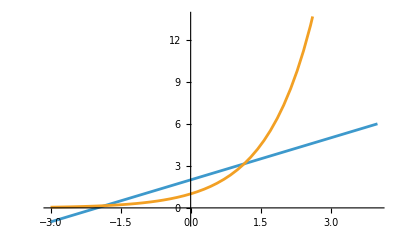

{x→1.14619}

```mathematica
(*An example of using FindRoot to solve a trancendental equation  *)
Plot[{x+2,Exp[x]},{x,-3,4}] (*A plot to visualize where the solutions are we will go over plots in section 3*)
FindRoot[Exp[x]==x+2,{x,1}] (*an example with the FindRoot to find the solution near x = 1*)
```

There is also a numerical differential equation solver which we will look more at in section VI .

### Units in Mathematica

To end this section, we are going to go over how you can use units in Mathematica. Mathematica has a lot of built-in units. The way you can make use of them is using the Quantity[<Magnitude>,”<UnitName>”] command:

```mathematica
Clear["`*"]
m = Quantity[10,"Kilograms"] (*define a mass of 10 kg*)
```

Mathematica can use compound units and will correctly handle units when doing calculations. It can even handle unit conversions:

```mathematica
g = Quantity[32.2,"Feet"/"Seconds"^2] (*Define the acceleration due to gravity on Earth to be 32.2 ft/s^2*)
```

```mathematica
(*Convert g to m/s^2*)
UnitConvert[g, "Meters"/("Seconds")^2]
```

```mathematica
(*Calculate the weight of a 10 kg mass on Earth*)

weight = m g

(*Convert the weight to Newtons and pounds*)

UnitConvert[weight,"Newtons"]

UnitConvert[weight,"PoundsForce"]
```

The unit calculations are not fool-proof however, and sometimes you will need will want to just extract the magnitude or the units themselves this can be done using the QuantityMagnitude and QuantityUnit command.

```mathematica
QuantityMagnitude[g] (*get the magnitude of g (32.2)*)
QuantityUnit[m] (*get the unit of m (Kilograms)*)
```

You can also define your own units, but that is outside the scope of this notebook.

#### Wolfram|Alpha shortcuts

For this section, you will want to ensure Dynamic Updating is enabled, see Section 0 for instructions on how to do this.  You have probably used or seen WolframA|lpha to help with homework from time to time. If you have Dynamic Updating enabled, you can access the WolframAlpha directly in Mathematica. You can open a Wolfram|Alpha prompt by pressing “Ctrl + =” in an input cell this will cause a dialog box to appear with an orange equals sign: -Graphics-. Using this you can lookup constants and generate code (though I would be wary of the code generation).  You can also write a quantity with units to shortcut defining quantities. For example, by typing “permittivity of free space”, I can get the constant ϵ_0:

```mathematica
ϵ0 =  (*permittivity of free space*)
```

And by writing “10 V” I can get a quantity representing 10 Volts

```mathematica
V =
```

Another cool feature of this is that even if you have a typo in what you are trying to get, Mathematica may still be able to figure it out. Again, however, this is not fool-proof. The check-mark next to the box is their for you to confirm that Mathematica’s interpretation of what you wrote is correct. There is a large amount of information that Wolfram|Alpha has access to, so if there is a constant or something you need, just try searching for it in Mathematica:

```mathematica
(*This is what happens when I ask for an image of a dog*)
```

```mathematica
(*here is an example of when I ask to generate code, I asked it to generate a plot of sin(x)*)
```

#### Exercise

For this exercise, I am going to ask you to solve a basic conservation of energy problem:
A ball of mass 20 g is dropped from a height of  = 10 ft. After the ball hits the ground, it bounces to a max height of  Calculate 
(a) The total energy (in Joules) of the ball before it is dropped
(b) The speed of the ball (in m/s) as it hits the ground
(c) The total energy of the ball after it hits the ground

```mathematica
(*Your code here*)
```

#### Solution

For (a), we need only calculate the initial gravitational potential energy

```mathematica
Clear["`*"] (*Clear constants*)
(*define constants*)
g = ;
m = Quantity[20, "Grams"];
h = ;

E0 =UnitConvert[ m g h ,"Joules"]// N(*initial energy in Joules*)
```

For  (b), we can simply use the formula for kinetic energy to find the speed

```mathematica
v/. Solve[E0 == 1/2 m v^2,v]//UnitConvert (*this will produce both the positive and negative solution*)
```

For (c), we simply do a similar calculation as we did for a, but with 1/3 the height

```mathematica
Ef = UnitConvert[ m g h/4 ,"Joules"]// N (*final energy in Joules*)
```

## III. Plotting and Graphics

In this section we are going to go over some basic graphical features that Mathematica, including plots, primitive graphics, and animations.

### 1D Plots and Plot Options

Perhaps one of the most useful features of Mathematica is its ability to produce plots and graphics suitable for presentations and publications. Let’s begin with simple 1D plots, these are made using the Plot command. The basic syntax is Plot[<function>, {<variable>,<min>,<max>}]. The function can also be user-defined, you just need to make sure that the variable we are plotting against is the same as the function. Below is a plot of the function  + sin(2 π x)

```mathematica
Clear["`*"]
f[x_]:= Cos[π x] + Sin[2 π x] (*user defined function *)
Plot[f[x],{x,-2,2}] (*plot of function*)
```

You can even plot multiple functions in the same Plot command:

```mathematica
g[x_]:= Cos[2π x] + Sin[π x] (*another user defined function*)
Plot[{f[x],g[x]},{x,-2,2}] (*plot both of the user-defined functions together*)
```

While it is nice that Mathematica changes the color of each function, in this particular case it is kind of difficult to tell which function is which without some careful thought. Fortunately, we can make use of plot options to label the different functions. To implement plot options, we have to include them after the domain specification, separate each option by a comma, and and use the arrow syntax as follows: 
Plot[<function and domain info>, PlotOption1 -> <value1>, PlotOption2 -> <value2>, ...]. 
As an example, we will use the PlotLegends option on the previous plot.

```mathematica
Plot[{f[x],g[x]},{x,-2,2},PlotLegends->{"f(x)","g(x)"}]
```

Notice, if you are plotting multiple functions, you can adjust the plot option for each function by using a bracketed list { <function1 option val>, <function2 function val>, ...}. 
While this is great for trying to visualize plots for personal use, the above plot is hardly appropriate to put in a reports, publications, or presentations.

#### Plot Options for Formatting

Here are a list of plot options that may be useful to tidy up plots, you will have to check the documentation to see what values are appropriate for each option.
	PlotRange: Allows you to change how much of the plot you can see within the plot window
	PlotLabel: Gives the plot an overall label
	LabelStyle: Allows you to edit the font of the label
	PlotLabels: Individually labels each function plotted
	ColorFunction: Changes the plot color based on the values of the function
	AxesLabel: Labels the axes
	AxesStyle: Allows you change the style of the axes
	PlotStyle: Allows you to edit the color, thickness, plot points, and style with which Mathematica plots the function
	PlotLegends: Creates a Legend for the plot
	Background: Allows you to change the color of the background
	Ticks: Allows you to change the plot ticks and scale along the axes
	Frame: Puts a frame around the plot
	FrameLabel: Allows you to label the frame
	FrameTicks: Allows you to change the Frame ticks
	FrameStyle: Allows you change the style of the frame
	GridLines: Allows you to put gridlines on your plots

Below are some examples of what can be done with some of these plot options, feel free to mess around with the values or add your own to see how it works

```mathematica
Clear["`*"] (*clear all variables*)
 (*Some user defined functions*)
f[x_]:= Exp[x]Sin[x];
g[x_]:= Exp[-x]Cos[x];
h[x_]:= Sin[x]Cos[x];
```

```mathematica
Plot[{f[x],g[x],h[x]},{x,-π,π},PlotRange->Automatic,Background->White,PlotLegends->{"f(x)","g(x)","h(x)"},PlotStyle->{{Red,Dashed},{Blue,Dotted},{Green,Thick}}, AxesLabel->{"x","y"},AxesStyle->Directive[Black, Bold], PlotLabel->"Plot of some Functions", LabelStyle->Directive[Bold, Black]]
```

```mathematica
Plot[g[x],{x,-π,π},PlotRange->{-8,5},Background->White,AxesStyle->Directive[Black, Bold], PlotLabel->"Plot of a Function", LabelStyle->Directive[Bold, Black],Frame->True,FrameStyle->Directive[Black,Bold],FrameLabel->{"Independent Variable", "Dependent Variable"},GridLines->Automatic,ColorFunction-> "TemperatureMap"]
```

Another thing to keep in mind is the scale of your plots, the command LogPlot, LogLinearPlot, and LogLogPlot, allow you to use a Logarithmic scale on one or both of the axes:

```mathematica
LogPlot[Exp[x],{x,0,10}] (*Log plot scales the y-axis, logarithmically*)
```

```mathematica
LogLinearPlot[Log[x],{x,0,10^4}] (*LogLinearPlot scales the x-axis, logarithmically*)
```

```mathematica
LogLogPlot[x^x,{x,0.1,10}] (*LogLogPlot scales both axes, logarithmically*)
```

#### Nuances of Plot Commands

The Plot and other plotting commands use numerical calculations to make plots. Therefore, just like with other numerical commands, there are some options you can use to improve the accuracy and quality of your plots. The way that Mathematica plots is by sampling values in the domain specified and then uses recursive subdivisions to fill in the gaps between the sampling points. Typically, Mathematica does a good job of choosing the number of sampling points and recursive subdivisions automatically, but occasionally you may need to adjust these values for more complicated functions.  

As an example we are going to take a look at the truncated Fourier series for a Dirac delta function, here is code to initialize such a function:

```mathematica
Clear["`*"]

f[x_]=FourierSeries[DiracDelta[x],x,50]; (*generated the first 50 terms of a Fourier series for a dirac delta function (this may take a while to execute)*)
```

This function is highly oscillatory, so if I tell Mathematica not to use any recursive subdivisions using MaxRecursion -> 0, we get a rather jagged plot:

```mathematica
Plot[f[x],{x,-1,1},PlotRange->All, MaxRecursion->0] (*a plot which uses zero recursive bisections*)
```

However, I can remedy this by increasing the number of plotting points using PlotPoints:

```mathematica
Plot[f[x],{x,-1,1},PlotRange->All,PlotPoints->1000,  MaxRecursion->0]
```

I can also alternatively have small amount of plotting points and increase the number of recursive subdivisions,

```mathematica
Plot[f[x],{x,-1,1},PlotRange->All,PlotPoints->10, MaxRecursion->10]
```

Feel free to mess around with the numbers to see how the plot changes.

However, as stated before, Mathematica’s default is to automatically determine an appropriate amount for both PlotPoints and MaxRecursions. So, you can usually omit having to mess with these options:

```mathematica
Plot[f[x],{x,-1,1},PlotRange->All]
```

In cases of complex numerical models, however, you may find that your plots are not turning out the way you would like. In these cases, consider changing some of these values. There are also options like Exclusions which works similar to the NIntegrate equivalent. You will likely have to look into the different options as you run into issues and learn with experience. 

Another thing to note with plots is that they can handle quantities (i.e things with units), however, they will only plot the magnitudes without any units involved so be wary of what units your variables have.

```mathematica
a = ; (*acceleration of 2 m/s^2*)
F[x_]:= Quantity[x,"Kilograms"] a; (*force for an object of mass x*)
Plot[F[x],{x,0,10}] (*A plot which is gives the force in Newtons as a function of the mass in kg, but there is no indication as to what the units are*)
```

### Plots in Higher Dimensions

Mathematica also has a variety of options for displaying plots in higher dimensions. A lot of the plot options from before also apply to these plots, though you may have to look in the documentation to see how they work for each kind of plot. The rest of this section just highlights some useful plot commands with some examples. Keep in mind that it usually takes more computing power to render 3D graphics and you may be better off using a different representation.

#### Plot3D

Plot3D allows you to visualize surfaces, note that with 3 D plots, you can use your mouse to click and drag to change the view of the plot . Commands like ViewPoint can also change at which view the plot is oriented to begin with .

```mathematica
f[x_,y_]:= x^2 Sin[y]
Plot3D[f[x,y],{x,-5,5},{y,-5,5},ViewPoint-> Top] (*A plot of x^2 Sin[y]*)
```

#### Contour Plots

ContourPlot is a great way to visualize a surface without using 3D graphics, adding a color function and a legend can help make it more readable. You can also use it to plot solution curves.

```mathematica
ContourPlot[Cos[x]Sin[y],{x,-2π,2π},{y,-2π,2π},ColorFunction->"DeepSeaColors",PlotLegends->Automatic] (*A plot of the surface f(x,y) = Cos[x]Sin[y]*)
```

```mathematica
ContourPlot[x^2 + y^2 == 4, {x,-3,3},{y,-3,3}] (*Plot of solutions to x^2 + y^2 = 4*)
```

There is also a 3D version:

```mathematica
ContourPlot3D[x^2+y^2+z^2==4,{x,-2,2},{y,-2,2},{z,-2,2}]
```

#### Vector Fields

VectorPlot and StreamPlot are useful for displaying vector fields:

```mathematica
Clear["`*"]
Efield[x_,y_]= 1/(Sqrt[x^2+y^2]^3){x,y};(*a simple 2D Electric field for a positive charge at the origin*) 
VectorPlot[Efield[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
V[x_,y_]= x^2+y^2; (*A simple 2D potential*)
GradV[x_,y_]= Grad[V[x,y],{x,y}]; (*get the gradient of V*)
StreamPlot[-GradV[x,y],{x,-4,4},{y,-4,4}]  (*Plot of *)
```

There is also a 3D version of both of these

```mathematica
Clear["`*"]
Efield3D[x_,y_,z_]= 1/(Sqrt[x^2+y^2]^3){x,y,z};(*a simple 3D Electric field for a positive charge at the origin*) 
VectorPlot3D[Efield3D[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]
```

```mathematica
V[x_,y_,z_]= x^2+y^2+z^2; (*A simple 3D potential*)
GradV[x_,y_]= Grad[V[x,y,z],{x,y,z}]; (*get the gradient of V*)
StreamPlot3D[-GradV[x,y],{x,-1,1},{y,-1,1},{z,-1,1}]  (*Plot of *)
```

#### Parametric Plots

ParametricPlot allows you to plot parametric curves like that of a projectile:

```mathematica
(*Projectile motion*)
Clear[x,y];
v =20; (*launch speed*)
g = 9.8;(*acceleration due to gravity*)
θ = 30 Degree; (*launch angle*)
(*kinematic equations*)
x[t_]= v Cos[θ]t; 
y[t_] = v Sin[θ]t - 1/2 g t^2;
(*Parametric Plot of the trajectory*)
ParametricPlot[{x[t],y[t]},{t,0,4},PlotRange->{{0,40},{0,6}}]
```

Again, there is a 3D equivalent to this:

```mathematica
(*Motion of a charged particle through a uniform magnetic field*)
Clear[x,y,z];
v =0.5; (*initial speed*)
R=1;(*Radius of orbit*)
ω =5; (*angular frequency*)
(*kinematic equations*)
x[t_]= R Cos[ω t]; 
y[t_] = R Sin[ω t];
z[t_]=v t;
(*Parametric Plot of the trajectory*)
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,4}]
```

#### Complex Functions

For complex functions, you can use Re and Im to extract the imaginry and real components of complex numbers to plot separately:

```mathematica
Plot[{Re[E^(I θ)],Im[E^(I θ)]},{θ,-π,π},PlotLegends->"Expressions"]  (*ends up plotting  and *)
Compl
```

However, this still doesn’t really help us visualize mapping a complex number to another complex number. ComplexPlot and ComplexPlot3D utilize color to represent the Argument of a complex number. This can help better visualize complex numbers.

```mathematica
Clear[w,z]
w[z_]:= Exp[1/z]/((z+2)(z+1)^2) (*a complex function*)

ComplexPlot[w[z],{z,-3-3I,3+3I},PlotLegends->Automatic]
ComplexPlot3D[w[z],{z,-3-3I,3+3I},PlotLegends->Automatic]
```

### Graphic Primitives and Combining Graphics

Mathematica has a wide variety of graphics objects available for use.  Strictly speaking, the plots we have already done are graphics objects. In this section, however, we are going to go over graphics primitives. The implementation of these graphics can get pretty cumbersome and complicated, so we will only go through a basic example using 2D graphics, just know that 3D versions also exist. Don’t hesitate to check the documentation if you are unsure how something works. 

Graphics primitives are commands that you can call to create different graphics objects. You can store these objects in variables, but in order to tell Mathematica how to actually display them you need to use the Graphics (or Graphics3D) command.

```mathematica
disk1 = Disk[{1,0},0.25] ;(*this will create a disk of radius 0.25 at the the coordinate (1,0) *)
Graphics[disk1]  
(*this will display the disk*)
```

Since this disk is on it’s own, you can’t really tell that it is a disk of radius 0.25 at (1,0). Fortunately, we can include multiple objects in the Graphics command:

```mathematica
disk2 =  Disk[{-1,0},0.5]; (*create a different disk at (-1,0) with radius 0.5*)

Graphics[{disk1,disk2}] (*display the two disks*)
```

In order to change the formatting and style of the graphics object, we actually need to create a list and include all of our options we want to apply before listing our graphics object. The Directive command one way to include all of the format changed we want into a single command:

```mathematica
arrow1 = {Directive[Red,Thick],Arrow[{{-1,0},{-0.5,0}}] };  (*Create a red centripetal force vector*)
text1 = {Directive[Red,Thick], Text["",{-0.75,0.1}]};  (*create text to label the force vector*)
circle = {Directive[Blue,Dashed],Circle[{-0.25,0},0.75]}; (*create a blue dashed circle to trace out the orbit*)
object= {Black,Disk[{-1,0},0.1]} ;(*create a disk representing an object in uniform circular motion*)
arrow2 = {Green,Arrow[{{-1,0},{-1,-0.3}}]}; (*vector representing the tangential velocity*)
text2 = {Directive[Green,Thick], Text["",{-1.2,0}]}; (*label for the tangential velocity*)

Graphics[{circle,arrow1,text1,arrow2,text2,object}] (*The last object in a list will be drawn on top of the existing objects*)
```

As another note, a lot of graphics primitives can also represent Mathematical objects such as a curve, region, or contour of integration:

```mathematica
unitCircle= Circle[];

ContourIntegrate[1/z,z ∈ unitCircle] (*preform a complex contour integral over the unit circle in the complex plane of the function 1/z*)
```

Combining graphics primitives together can make for some good visuals, but what if you want to combine a graphics primitive to something like a plot? Fortunately, you can use the Show command to do just that. The Show command will simply put all of our graphics objects on a single canvas. Note, however, if you choose to use multiple plots in Show, only the formatting options in the first graphics object will take priority, though you can change some of these in the Show command.

```mathematica
parabolaPlot = Plot[x^2,{x,-.8,.8}, Background->White, PlotLabel->"Mean Value Theorem Example, ", LabelStyle->Directive[Bold, Black],FrameStyle->Directive[Black, Bold], Frame->True,AxesStyle->Directive[Black, Bold]]; (*plot of a prabola*)
points = {Red,Point[{{0.6,0.6^2},{-0.6,0.6^2}}]}; (*Red endpoints A and B*)
greenPoint = {Green,Point[{0,0}]}; (*green zero point C*)
text1 = {Red, Text["A",{-0.55,0.6^2+.05}]}; (*text for point A*)
text2 = {Red, Text["B",{0.55,0.6^2+.05}]}; (*text for point B*)
ABslope = {Red, Line[{{0.6,0.6^2},{-0.6,0.6^2}}]}; (*line representing slope from A to B*)
zeroSlope = {Green, Thick,Line[{{-0.2,0},{0.2,0}}]}; (*Line representing derivative at point C*)
text3 = {Green,Text["C",{0,0.05}]}; (*text for point C*)

primitives = Graphics[{points, greenPoint,text1,text2,ABslope,zeroSlope,text3}]; (*store the graphics primitives on a single canvas*)

Show[parabolaPlot,primitives](*Use Show command to combine graphics*)
```

#### Exercise

In the input cell below, I have defined the function V, which represents a 2D electric potential for two point charges. Create a plot which shows both the electric field lines and the equipotential contour lines. Make sure your plot is appropriately labeled.

```mathematica
Clear["`*"]
V[x_,y_]:= 1/(((x-1)^2+(y-1)^2)^(3/2))- 1/(((x+1)^2+(y+1)^2)^(3/2))(*2D potential*)
(*Your code here*)
```

#### Solution

We can use the ContourPlot command to get the equipotential lines, since we only want the equipotential lines, we are going to turn the shading off.  Since I want the field lines to go over the equipotential lines, I am going to add all my formatting options to this plot

```mathematica
V[x_,y_]:= 1/(((x-1)^2+(y-1)^2)^(3/2))- 1/(((x+1)^2+(y+1)^2)^(3/2))(*2D potential*)
equipotentialcontours = ContourPlot[V[x,y],{x,-3,3},{y,-3,3},ContourStyle->Black, ContourShading->None, Background->White, AxesStyle->Directive[Black,Bold],LabelStyle->Directive[Black,Bold],PlotLabel->"Electric Field Generated by ", FrameStyle->Directive[Black,Bold], FrameLabel->{"x","y"}]
 (*Contour plot for equipotential lines*)
```

For the electric field lines, I am going to use StreamPlot, though VectorPlot would also work. I will omit any formatting options as I have already took care of them in my contour plot:

```mathematica
Efield[x_,y_]= -Grad[V[x,y],{x,y}];(* calculate the Efield by *)
linesPlot = StreamPlot[Efield[x,y],{x,-3,3},{y,-3,3}]
```

I can then use the Show command to display the two plots:

```mathematica
Show[equipotentialcontours,linesPlot]
```

### Animations and Exporting Graphics

#### Manipulate and Animate

Another way to generate useful visuals in Mathematica are the Manipulate and Animate commands. The Manipulate command allows you to add sliders to your plots, allowing you to adjust values and see how this influences your plot. Keep in mind that Mathematica will need to calculate as you change the parameters and the complexity of your calculation may require extra time to generate a result.

```mathematica
Manipulate[Plot[Sin[a x+b],{x,0,6},PlotLabel-> "Plot of sin(ax+b)"],{a,1,4},{b,0,10}] (*a manipulatable plot of *)
```

By clicking the + by each variable you can input specific values and even play an animation which will vary the specific variable.

This will work on things other than plots as well:

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}] (*will factor x^n+1)*)
```

The Animate command is great when trying to visualize something moving in real time. For example, let’s look at a traveling wave solution to the wave equation:

```mathematica
Animate[Plot[Cos[x - t],{x,0,5}, PlotRange->{-1,1}],{t,0,10},AnimationRunning->False]
```

Note, the AnimationRunning -> False option will prevent the animation from running upon execution. Similarly to the manipulate command, the frames of the animation are not calculated until they are needed. If I did not include this option, the animation would continually calculate the frames until you tell it to stop. Unfortunately, the Animate command is quite resource intensive. Since we are calculating enough frames for a smooth animation, this requires a lot of computing power and can take up a lot of your computers resources if you are not careful. Fortunately, there is a way to get around us by creating a collection of images and exporting the files as a gif.

#### Exporting Graphics

Before exporting anything, we will need to make sure we know where the files are going. We can do this using the SetDirectory command. Right now, the below command will set this to whatever your default documents directory is. However, you can also use SetDirectory[NotebookDirectory[]] to have the files export to the same folder that this notebook is contained in. You may change the below so that the files we export go to the directory you would like. If you are unsure what to do, just use SetDirectory[NotebookDirectory[]]. Make sure you execute the code below.

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

Before we create a gif, let’s first show how to export a simple image graphic. Below is code from earlier in the section, visualizing the Mean Value Theorem:

```mathematica
parabolaPlot = Plot[x^2,{x,-.8,.8}, Background->White, PlotLabel->"Mean Value Theorem Example, ", LabelStyle->Directive[Bold, Black],FrameStyle->Directive[Black, Bold], Frame->True,AxesStyle->Directive[Black, Bold]]; (*plot of a prabola*)
points = {Red,Point[{{0.6,0.6^2},{-0.6,0.6^2}}]}; (*Red endpoints A and B*)
greenPoint = {Green,Point[{0,0}]}; (*green zero point C*)
text1 = {Red, Text["A",{-0.55,0.6^2+.05}]}; (*text for point A*)
text2 = {Red, Text["B",{0.55,0.6^2+.05}]}; (*text for point B*)
ABslope = {Red, Line[{{0.6,0.6^2},{-0.6,0.6^2}}]}; (*line representing slope from A to B*)
zeroSlope = {Green, Thick,Line[{{-0.2,0},{0.2,0}}]}; (*Line representing derivative at point C*)
text3 = {Green,Text["C",{0,0.05}]}; (*text for point C*)

primitives = Graphics[{points, greenPoint,text1,text2,ABslope,zeroSlope,text3}]; (*store the graphics primitives on a single canvas*)

NVTgraphic =Show[parabolaPlot,primitives](*Use Show command to combine graphics*)
```

I saved the output from the Show command, variable MVTgraphic. I can then Export this to my directory using the Export command. The syntax is Export[“<filename.extension>”,<object>]. This will export the object into the directory we set earlier with file name “filename” and the extension ”.extension”.  We can export our mean value theorem graphic as a jpeg using the command below:

```mathematica
Export["MVT.jpg",MVTgraphic]
```

You can check your directory to open the new image and we can likewise open this graphic using SystemOpen:

```mathematica
SystemOpen["MVT.jpg"]
```

Note if you export to an already existing file, this will overwrite the existing file so be careful to not write over important files. 

Now, lets take advantage of how the gif file extension works so our animations take up less computing resources and can actually be exported and used in demonstrations/presentations. To do this, rather than using the Animate command, we are going to use the Table command to create a list of graphics. This list will contain all of the frames we want to use in our animation. Again, we will use our traveling wave example:

```mathematica
animationframes = Table[Plot[Cos[x - t],{x,0,5}, PlotRange->{-1.1,1.1}, PlotLabel->", t = "<>ToString[t] <>" s."],{t,0,10,0.1}]; (*This will calculate and store all the frames of our animation at once, obviously the more frames means the smoother the animation will look make sure to use a semi-colon to supress output*)
```

While this may take a minute to generate all of the frames, unlike with the Animate command, you only need to do this once rather than continuously having to calculate these frames when required. We can then just simply export our animation frames with the .gif extension and we can then view our animation by opening the gif:

```mathematica
Export["Wave.gif",animationframes] (*Creates a gif*)
```

```mathematica
SystemOpen["Wave.gif"] (*Open the gif*)
```

This allows you to only have to do heavy computations one time in order to view the animation and you now have a file that you can use for presentations and sharing.

## IV. Programming Techniques and Tools (WIP)

This section will go over Mathematica’s flavor of the programming techniques and tools that are common across most programming languages. This includes things like logic, modules, packages, and debugging.

### Logic: Conditionals, Loops, and Prompts

Like most programming languages, Mathematica also contains boolean variables and logic. In Mathematica, booleans can have a truth value of True or False (though sometimes statements can return as neither).  These are pre-defined symbols that you can assign to variables. You can also turn booleans into values by using Boole:

```mathematica
Boole[True] (*Returns 1*)
Boole[False] (*Returns 0*)
```

You can also write Mathematical statements using logical operators and Mathematica can evaluate them as True, False, or undetermined. When an output is undetermined, Mathematica failed to assign a truth value and will usually just return the input. Below are some cells with common logical operators:

==, the is equal to operator. Compares two expressions and returns True if they are equivalent and false otherwise

```mathematica
1 == 2 (* returns false because 1 != 2, note you can't use a single = since this will try to assign a variable*)
(x+1)^2 == x^2+2x + 1  // Simplify(*returns true. also works for different forms of expressions, though you may need to use Simplify*)
```

False

True

< less than, >greater than, >= greater than or equal to, <= less than or equal to. These are comparison operators between numbers, returns True if the comparison is true.

```mathematica
1 >0 (* Returns true becasue 1 is greater than 0 *)
1>= 3 (*returns false because 1 is not greater than or equal to 3, note that when you type > and then =, it will automatically turn into >=*)
Clear[a,b]
a>b (*Mathematica simply returns the statement a>b since neither are defined and Mathematica cannot determine a truth value for the statement *)
```

True

False

a>b

!, logical not operator. You can combine this with other logical operators to negate them.

```mathematica
1 != 2 (*returns true because 1!=2, typed by writing ! and then =*)
```

&& logical and operator. This allows you to combine multiple statements, will only evaluate True if all statements are True. You can also use the character “∧” by pressing Esc, typing “and”, and hitting Esc again.

```mathematica
1 ==1 && 2 == 2 ∧ 3 == 3 (*returns true because 1=1, 2=2, and 3=3 are all true statemens, you can use both && and ∧ in the same statement*)
```

True

|| logical or operator. This also allows you to combine multiple statements, will evaluate True if at least one of the statements involved is True. You can also use the character “∨” by pressing Esc, typing “or”, and hitting Esc again.

```mathematica
1 ==0 || 1== 1|| 1 == 2  (*evaluates true because 1=1, even though the other statements are false*)
```

True

There are also some other of the less common, though useful logical operators such as Xor and Nor, check the documentation for information on these logical operators.

#### Conditionals

Like other programming languages, Mathematica can use conditional statements that will only execute code if a condition is met. The If conditional has the syntax If[<condition>,<true output>,<false output>].

```mathematica
If[EvenQ[4], "4 is even", "4 is odd"] (*outputs string "4 is even", EvenQ returns true if the input is even*)
If[EvenQ[3],"3 is even", "3 is odd"] (*outputs string "3 is odd"*)
```

4 is even

3 is odd

Since you can put undefined variables in a statement, you can add an additional output if Mathematica fails to assign a truth value to the condition:

```mathematica
Clear[a,b]

If[a<b,"a is less than b","a is not less than b","Either a or b are not defined, please make sure they have definite values."] (*prints out the last string since we have defined a or b, and Mathematica cannot assign a truth value*)
```

Either a or b are not defined, please make sure they have definite values

If you have more than two possibilities for you conditions, you will have to use the Switch statement. This has the syntax Switch[<expression>,<form_1>,<value_1>,<form_2>,<value_2>, ...]. Switch will only evaluate the first met condition:

```mathematica
Switch[{EvenQ[4], IntegerQ[4]},


]
```